## SimAnimate-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 14:30:58
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
<<xlr8r.m
```

xCellerator 0.95 (28-Feb-2014) loaded Wed 14 Jun 2017 14:31:00
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

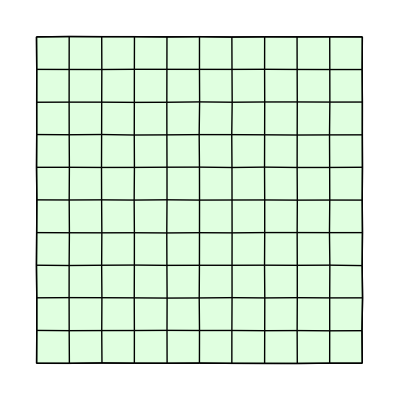

```mathematica
w=TemplateRectangular[10,10];
w=RandomizeTemplate[w, 0.01];
ShowTissue[w]
```

## The following network is a mass-action implementation of the simple harmonic oscillator.

```mathematica
net = {{X+Y-> X, k1/Y[t]}, {Y-> Y+X, k2}};
parameters = {k1-> 1, k2-> 1}; 
interpret[net]/.parameters
```

{{X'[t]==Y[t],Y'[t]==-X[t]},{X,Y}}

```mathematica
s=run[net/.parameters, initialConditions-> {X-> 1, Y-> 1}, timeSpan-> 10]
```

{{X→InterpolatingFunction[{{0., 10.}}, <>],Y→InterpolatingFunction[{{0., 10.}}, <>]}}

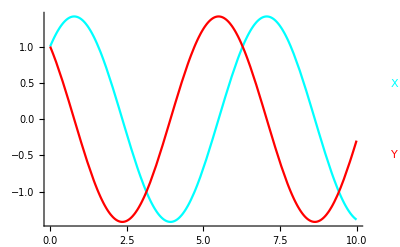

```mathematica
runPlot[s]
```

## Extend the network to the template with diffusion, and run a simulation

```mathematica
bignet=CelleratorNetwork[w, "Reactions"-> net, "Diffusion"-> {{X, DX}}];
```

100 Cells.

2 internal reactions in each cell.

200 intracellular reactions.

100 Cells.

2 internal reactions in each cell.

200 intracellular reactions.

360 diffusion reactions.

560 total reactions.

```mathematica
myic=Table[{X[i]-> RandomReal[{-1,1}], Y[i]-> RandomReal[{-1,1}]}, {i, 1, 100}]//Flatten;
```

```mathematica
sim=RunSim[bignet/.{DX-> .5}, parameters, myic, {0,40}];
```

#### SimPlot plots the value of X[i][t] for very cell. Though they values start off different, they all approach synchronicity because of the diffusion.

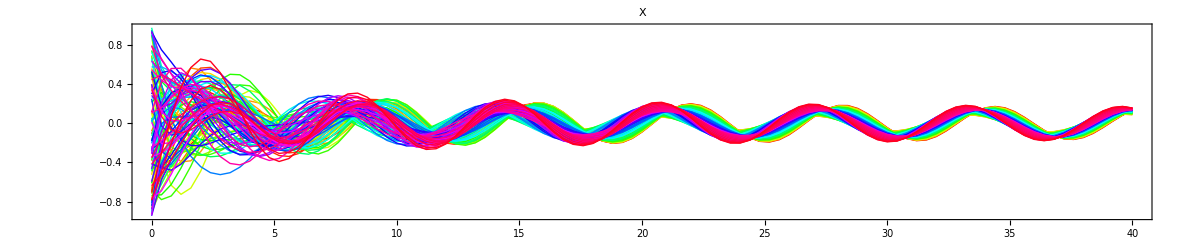

```mathematica
SimPlot[sim,X, AspectRatio-> .2, ImageSize-> 1200]
```

## Show X across the template at the final time step

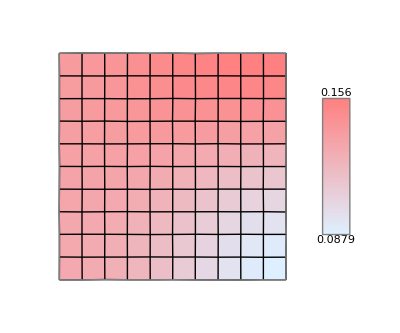

```mathematica
SimShowFinal[sim,X, w, {LightBlue, Pink}]
```

## use SimAnimate to generate a sequence of plots of X across the template

```mathematica
s=SimAnimate[sim, X, w, {0, 40, .5}, {LightBlue, Pink}, {0, .25}];
```

The plots can be viewed as an animation

```mathematica
ListAnimate[s]
```

## save images to generate a move file

```mathematica
SaveFrames[s, "jpg", 300, "mov","simanimate-example"]
```

Created folder: /Users/mathman/Cellzilla/Simulations-14-Jun-17/simanimate-example14Jun17-1444

movie file will be: simanimate-example14Jun17-1444.mov

movie file will be in the folder: /Users/mathman/Cellzilla/Simulations-14-Jun-17/simanimate-example14Jun17-1444

Created directory: /Users/mathman/Cellzilla/Simulations-14-Jun-17/simanimate-example14Jun17-1444/Frames

Putting movie frames in  in /Users/mathman/Cellzilla/Simulations-14-Jun-17/simanimate-example14Jun17-1444/Frames

ffmpeg -r 16 -i 'FRAME%4d.jpg' 'simanimate-example14Jun17-1444.mov'

ERROR: Unable to produce movie. ffmpeg return code is: 32512 On some versions of Mathematica (such as the version installed on this computer), the Kernel is unable to locate the correct path execute ffmpeg. You must do this manually:

In a command shell such as bash, terminal, or cmd, change your current working directory to (e.g., with the cd command):
 cd /Users/mathman/Cellzilla/Simulations-14-Jun-17/simanimate-example14Jun17-1444
Then type the following:
ffmpeg -r 16 -i 'FRAME%4d.jpg' 'simanimate-example14Jun17-1444.mov'
You can change the last field to whatever you want the movie to actually be called. In this case, it will be called simanimate-example14Jun17-1444.mov and be in the same folder as all the frames.